LinkObject[…]

0

01_VL d4is being analised

Table type 1

02_VL d6is being analised

Table type 1

03_VL d27is being analised

Table type 1

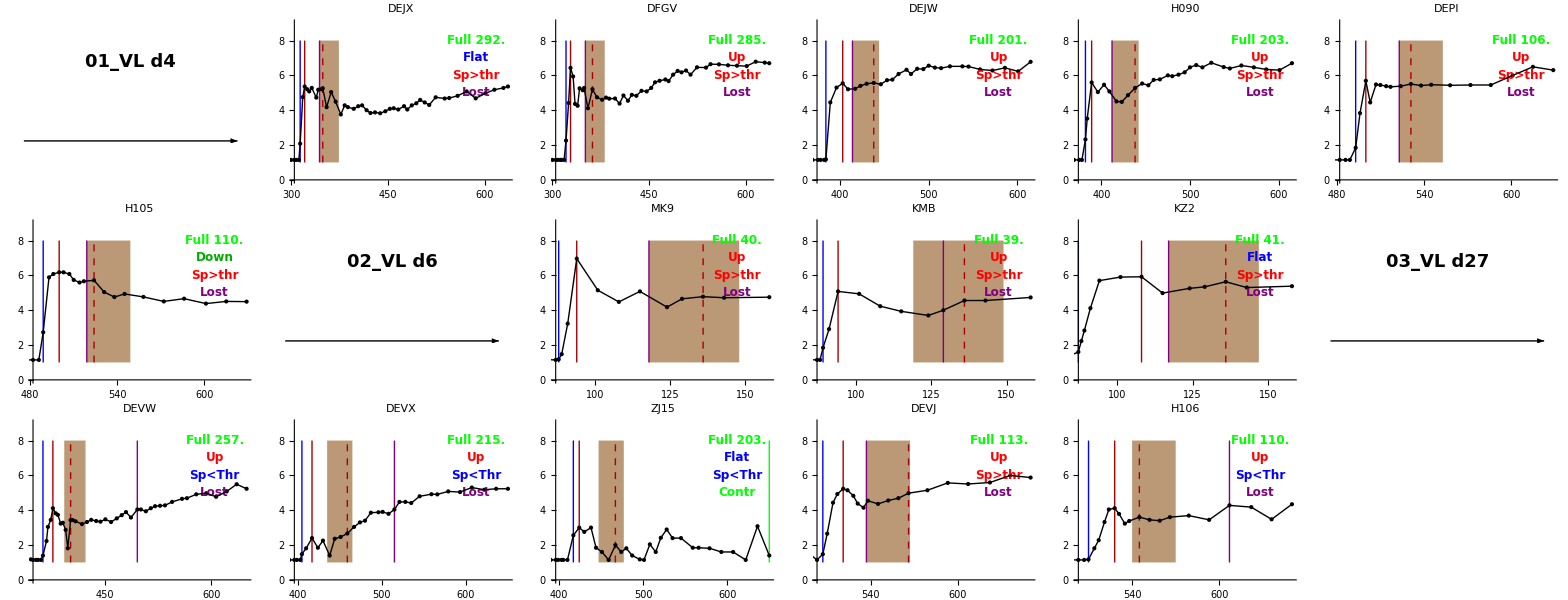

```mathematica
(*1. Set the parameters of the setpoint in the script by changing the constants under the parameters of the setpoint.
2. Run the code.
3. In the opened ‘Select file dialog’ window select one or multiple files with the input data.
4. In the opened ‘save file dialog’ enter the output file name.
5.By the default the output file will be in the same directory as the input files.
6. The level of the setpoint in the output Excel file are lines marked:'Continuous geometric mean setpoint VL' and 'Log of continuous geometric mean setpoint VL' in the ‘Stat’ spreadsheet.
The duration of control is in the ‘CtrScGrp’ spreadsheet.1-lost control,0-censored,code 2 and 3 means that the subject is not considered due to reasons discussed in the supplementary material.
*)


ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
<<JLink`;
InstallJava[];
ReinstallJava[JVMArguments->"-Xmx1024m"]

(*******************************Parameters of setpoint**************************************************)
(*!!!Const*) peaktime=30; (*time untill the start of setpoint*)
(*!!!Const*) setplength=30; (*duration of setpoint, can be longer than study, if integration to the end is needed*)
(*!!!Const*) cntrthr=10^4; (*Controler threshold*)

(*******************************Other Parameters**************************************************)
(*!!!Const*) StartInt=30; (*Strat of integration to setpoint*)
(*!!!Const*) toler=1/200; (*If the abs value of slope is less then this value than setpoint cosidered is flat*)
(*!!!Const*)sptype=0(* 1- the first measurement after or at setplength is the end of SP. 0- the last measur before or at  setpoint length is the end of SP*)
(*!!!Const*) xstep=1;


setptime=peaktime+setplength;

(******Pattern of missed values to delete in the data table and procedures accortin to input table types**********)
Pattern1={_Real,""};
Pattern2={"",""};
Pattern3={_Real,_String};

ReshapeTable1[data_]:=Module[{data1=data, data2={}},data2=Table[Transpose[{data1[[All,1]], data1[[All,i]]}],{i,2,Length[data1[[1]]]}];
data2=DeleteCases[data2,Pattern1,2];
data2=DeleteCases[data2,Pattern2,2];
data2=DeleteCases[data2,Pattern3,2]
];(*table formatted as {date,VL,VL....VL}, date column  or VL can be with gaps*)

ReshapeTable2[data_]:=Module[{data1=data, data2={}},data2=Table[Transpose[{data1[[All,i]], data1[[All,i+1]]}],{i,1,Length[data1[[1]]],2}];
data2=DeleteCases[data2,Pattern1,2];
data2=DeleteCases[data2,Pattern2,2];
data2=DeleteCases[data2,Pattern3,2]
]; (*table formatted as {date,VL,date,VL....date,VL}, date column and VL can be with gaps*)

(****************determines the slope of stpoint growths or decays***************************************)


Ifgrowth[data_,toler_]:=Module[{par={},sig=0,lm=0},If[Length[data]>1,
lm=LinearModelFit[data,x,x];
par=lm["BestFitParameters"];sig=If[Abs[lm[0]-lm[1]]<toler,0,Sign[par[[2]]]]; Join[{sig},par],
par={"ND","ND","ND"}
]
]; (**)
(**************************************************************************************************)

(****************reading the list of files***************************************)
fllength=0;
pathlist={SystemDialogInput["FileOpen",".xlsx"]};
pathlist=Flatten[pathlist,1];
If[pathlist=={"$Canceled"},fllength=0,fllength=Length[pathlist]];

(****************initialisation of global arrays and variables***************************************)
LogAprDatAll=LogInfDatAll=CtrScAll=allstat=grall={};
AllIDs={"Time -post detection" }; (* array for alligned VL*)
GlNSubj=0;(* countof subjects in ALL groups*)


For[filenum=1, filenum≤fllength,filenum++, (*Cycle through the list of files*)

namein=pathlist[[filenum]];
groupname=FileBaseName[FileNameTake[namein]];
Print[ groupname, "is being analised"];

grdiv=Graphics[{{{Arrowheads[Large],{Arrow[{{-3,1},{3,1}}]},Red}},Inset[Style[groupname,Black,Bold,18],{0,2}]}, ImageSize->{300,100}];(*divider of the graphics*)
AppendTo[grall,grdiv];

(***********************************Output names and INITIALISATION of arrays for the groups**********************************************)
(*!!!Const*) infstart={"VL at the first measurement >det. threshold (blue line)"};
(*!!!Const*) RelatDet={"Time of the first measurement >det. threshold (relative to the start of survey "};
(*!!!Const*) RelatDetAdj={"Time of the first measurement >det. threshold (relative to the start of survey  (day 0 -> day 0.01 for SC)"};
(*!!!Const*) SurveyStart={"Time 0f the start of the survey"};
(*!!!Const*) vldet={"VL at the first measurement above det. threshold"};

(*!!!Const*) maxvl1={"Max VL before setpoint (red line)"};
(*!!!Const*) maxvl2={"Max VL at setpoint (red dashed line)"};
(*!!!Const*) maxvltime1={"Time of the Max VL before setpoint"};
(*!!!Const*) maxvltime2={"Time of the Max VL at setpoint "};

(*!!!Const*) GeoMeanInt={"Continious geometric mean setpoint VL"};
(*!!!Const*) LogGeoMeanInt={"Log of continious geometric mean setpoint VL"};


(*Discrete setpoint, not used in the paper*)
(*!!!Const*) geomean={"Geom. mean"};
(*!!!Const*) med={"Median"};
(*!!!Const*) setpstart={"Setpoint start"};
(*!!!Const*) setpend={"Setpoint end"};
(*!!!Const*) lastspv={"Last value at setpoint "};
(*!!!Const*) trend={"Trend of setpoint"};
(*!!!Const*) spgrrate={"Setpoint grrate"};
(*!!!Const*) controller={"If geomen<"<>ToString[cntrthr]};

(*!!!Const*) complete={"If setpoint duration is >="<>ToString[setplength]};
(*!!!Const*) dursp={"Duration of the survey after the peak time of"<>ToString[peaktime]};
(*!!!Const*) numpsp={"Num of measurements at setpoint"};

(*!!!Const*) IntSP={"Integral of SP"};
(*!!!Const*) LogIntSP={"Log Integral of SP"};

(*!!!Const*) IntTail={"Integral " <>ToString[StartInt]<> " to Setp"};
(*!!!Const*) LogIntTail={"Log Integral " <>ToString[StartInt]<> " to Setp"};

(*!!!Const*) IntMaxTail={"Integral Max-End"};
(*!!!Const*) LogIntMaxTail={"Log Integral Max-End"};

(*!!!Const*) IntFullList={"Integral Last undet-Setp"};
(*!!!Const*) LogIntFullList={"Log of full Integrall"};

(*!!!Const*) CtrScGrp={{"Id","Abs time of event","Time relat. detection  ","1-lost, 0-censoured","Outcome", "Time relat. SP start"}};(*time-to loss-of-control summary *)
(***********************************************************************************)

(*!!!Const*) detvl=0;
(*!!!Const*) grphs=statout={};
(***********************************************************************************)

datraw=Import[namein];
data0=datraw[[1]];
 searchtime=Rest[datraw[[2,2]]];(*when start to search for the each individual*)
searchend=Rest[datraw[[2,3]]];(*how long to search for each individual*)
detthr=Rest[datraw[[2,4]]]; (*detection threshold separate for each individual. New to v30*)
If[!NumberQ[Last[detthr]] , detthr=Table[detthr[[1]],{i,1,Length[detthr]}] ];(*If only one detection threshold entered at pos 1, copying to other positions. New to v31*)
tableType=datraw[[2,5,2]];

(***********************************************************************************)
Which[tableType==1,data1=ReshapeTable1[data0];Print["Table type ", 1] ,tableType==2,data1=ReshapeTable2[data0];Print["Table type ", 2]];
data2=data1a=data1;(*data1a -will be with comments, extra line for subjects*)
(***********************************************************************************)


For[ nsubj=1, nsubj≤Length[data1], nsubj++,(* through all subjects*)
searchnum=spnum={};startinf=-1; AppendTo[data1a[[nsubj,1]],"Comment"];GlNSubj++;
MaxNMeasurInit=Length[data1[[nsubj]]];(* Max number of measurements in the patient, could be > searchtime*)
Id=data1[[nsubj,1,2]]; (*subject Id*) 


(*!!!Const*)CtrSc={Id,"","",4,"Controls",""}; (*By default do not loose control at the point*)


For[ nmeasur=2, nmeasur≤MaxNMeasurInit, nmeasur++,(* through all measur subj staring from second, header=1,*)
 AppendTo[data1a[[nsubj,nmeasur]],""];(* Adds the 3rd position to each patients record*)

If[data1[[nsubj,nmeasur,1]]≥searchtime[[nsubj]]&&(data1[[nsubj,nmeasur,1]]≤searchend[[nsubj]]),(*looking for initial search time. Start*)
 AppendTo[searchnum,nmeasur];(* if within time boundaries to search, save the position from all measurement, and search for  peack, sp etc*)

If[(data1[[nsubj,nmeasur,2]]>detthr[[nsubj]])&&(startinf==-1),startinf=nmeasur;data1a[[nsubj,startinf,3]]= "StartInf"]; (*start of infection*)

If[(data1[[nsubj,nmeasur,1]]≥data1[[nsubj,startinf,1]]+peaktime)&&(data1[[nsubj,nmeasur-sptype,1]]≤data1[[nsubj,startinf,1]]+setptime)&&(startinf!=-1),AppendTo[spnum,nmeasur]; 
(*Collecting all setpoint positions of measurement including the first point *)

];(*collecting data for stats within setpoint*)

(***************** time to loss of control Start************************)
If[nmeasur>3,(*at least 3 measurements*)
If[(data1[[nsubj,nmeasur-1,1]]≥data1[[nsubj,startinf,1]]+peaktime)&&(data1[[nsubj,nmeasur,2]]≥cntrthr)&&(data1[[nsubj,nmeasur-1,2]]≥ cntrthr)&&(CtrSc[[4]]≠1),

If[(data1[[nsubj,nmeasur-2,1]]≥data1[[nsubj,startinf,1]]+peaktime),
CtrSc={Id,data1[[nsubj,nmeasur-1,1]],"",1, "Lost",""},(*Case 1a, 2 measur. > trheshold, thre are measurement < threshold at ppt. *)
CtrSc={Id,data1[[nsubj,startinf,1]]+peaktime,"",1, "Lost",""} (*Case 1b, 1st and 2nd measur. after ppt > threshold, then lost at threshold *)
];
styleCont1=Purple]; (*1=event when subject loses control at 2 cosequetive measurement > threshold after the beggining of setpoint*)

] (*at least 2 measurements*)
(*******************Loss of control End***********************)

];(*looking for initial search time. End*)

]; (* through all measur in subj*)



MaxNMeasur=Last[searchnum] ;(*last measurement within searchtime*)
logdata1=Table[{data1[[nsubj,ii,1]],Log10[data1[[nsubj,ii,2]]]},{ii,2,Length[data1[[nsubj]]]}];(* Log10 of data1[[nsubj]], no header, case 2 in the description*)

(**************Aligning times to the first detection*******************************)
LogInfData1=Table[{logdata1[[nmeasur,1]]-logdata1[[startinf-1,1]],logdata1[[nmeasur,2]]},{nmeasur,startinf-1,Length[logdata1]}];
PrependTo[LogInfData1,{Id,""}];

InsPos=Flatten[Table[{j,2},{j,1,Length[LogInfData1]},{i,1,GlNSubj-1}],1];
LogInfData2=Insert[LogInfData1,"",InsPos];
AppendTo[LogInfDatAll,LogInfData2];
AppendTo[ AllIDs,ToString[Id]<>"*"<>groupname];
(*********************************************)


(*******time to loss of control**************************)
If[(data1[[nsubj,MaxNMeasur,1]]<=(data1[[nsubj,startinf,1]]+peaktime)),CtrSc={Id,data1[[nsubj,startinf,1]]+peaktime,"",2, "excl no sp",""};styleCont1=Orange 
];(* no points after the start at setpoint- exclude the subject*)

If[(data1[[nsubj,MaxNMeasur,1]]>=(data1[[nsubj,startinf,1]]+peaktime))&&(data1[[nsubj,MaxNMeasur-1,1]]<(data1[[nsubj,startinf,1]]+peaktime)), 
If[data1[[nsubj,MaxNMeasur,2]]>=cntrthr,CtrSc={Id,data1[[nsubj,startinf,1]]+peaktime,"",3, "ex 1pt>th",""};styleCont1=Orange ,CtrSc={Id,data1[[nsubj,MaxNMeasur,1]],"",0,"Contr",""}; styleCont1=Green]
(* If there are less than 2 points after the peak than censoured at time 0*)
];


If[(CtrSc[[4]]==4)&&(data1[[nsubj,MaxNMeasur,2]]≥ cntrthr),CtrSc={Id,data1[[nsubj,MaxNMeasur-1,1]],"",0,"Contr",""}; styleCont1=Green];(*Case 3 in the instruction. If not lost control but the last over the Treshold then cencoured at second last. *)
If[(CtrSc[[4]]==4)&&(data1[[nsubj,MaxNMeasur,2]]< cntrthr),CtrSc={Id,data1[[nsubj,MaxNMeasur,1]],"",0,"Contr",""}; styleCont1=Green];(*Case 2 in intsructions, If neither Lost nor Short and the last < threshold, then cesouring at last point*)

CtrSc[[3]]=CtrSc[[2]]-data1[[nsubj,startinf,1]]; (*aligning to the end of the peak*)
CtrSc[[6]]=CtrSc[[2]]-(data1[[nsubj,startinf,1]]+peaktime); (*aligning to the end of the peak*)
(*******time to loss of control**************************)

(*******trend after peak**************************)
If[(Length[spnum]>=1)&&(spnum[[1]]<MaxNMeasur),
{trnd,inetc, spgr}=Ifgrowth[logdata1[[spnum[[1]]-1;;MaxNMeasur-1]],toler], (*if Vl growth after peak *)
{trnd,inetc, spgr}={"ND","ND","ND"};
];
trndstr= Which[trnd==1,styleTrend=Red;"Up",trnd==-1,styleTrend=Darker[Green];"Down",trnd==0,styleTrend=Blue;"Flat",trnd=="ND",styleTrend=Black;"ND"];
(*******trend after peak**************************)

(*******Continious setpoint**************************)
If[(dur=data1[[nsubj,MaxNMeasur,1]]-(data1[[nsubj,startinf,1]]+peaktime))>0, (*If there are mesurements after peack, but not neceserarly there are points inside setpoint time*)

Clear[styleBar];
spbar={styleBar,Rectangle[{data1[[nsubj,startinf,1]]+peaktime,1},{data1[[nsubj,startinf,1]]+peaktime+setplength,8}]};(*  markin of setpoint continious*)

V=Interpolation[logdata1,InterpolationOrder->1]; (*interpolation of Log10 data*)

(************START OF Tabulating Interpolation function ****************)
LogAprDat=Table[V[x],{x,data1[[nsubj,startinf,1]],data1[[nsubj,MaxNMeasur,1]],xstep}]; (*Makean equal sample time for different datasets*)
PrependTo[LogAprDat,ToString[Id]<>"*"<>groupname];
AppendTo[LogAprDatAll,LogAprDat];
(*************END OF Tabulating Interpolation function***************)

(************START OF Integral of esposure ****************)

IntPtSetp= NIntegrate[ 10^V[x],{x,StartInt+data1[[nsubj,startinf,1]],data1[[nsubj,startinf,1]]+peaktime}];(* Integration from the givent point StartInt after detection to the start of setpoint*)
IntPtSetpLog=Log10[IntPtSetp];

IntFull=NIntegrate[10^ V[x],{x,data1[[nsubj,Max[startinf-1,2],1]],data1[[nsubj,startinf,1]]+peaktime}];(* Integration from last undetected to the start of setpoint*)
LogIntFull=Log10[IntFull];
(*************END OF Integral of esposure***************)

(************START OF Generalised Geometric mean of Set Point ****************)
int1=NIntegrate[10^ V[x],{x,data1[[nsubj,startinf,1]]+peaktime,Min[data1[[nsubj,startinf,1]]+ peaktime+setplength,data1[[nsubj,MaxNMeasur,1]]]}];(* Integratimg within setpoint*)
intLog=Log10[int1];

SPEnd=Min[data1[[nsubj,startinf,1]]+ peaktime+setplength,data1[[nsubj,MaxNMeasur,1]]]; (*end of setpoint, full or not full*)
int= NIntegrate[ V[x],{x,data1[[nsubj,startinf,1]]+peaktime,SPEnd}];(* Integration 0f Log data over continious setpoint*)

IntAverLog=int/(SPEnd-(data1[[nsubj,startinf,1]]+peaktime)) ;(* Log of Generalised Geometric mean*)
IntAverSp=10^IntAverLog;(*Generalised Geometric mean*)
(*************END OF Generalised Geometric mean of Set Point***************)
,

(*If Peaktime is not reached, no start of setpoint*)
IntAverLog=intLog=IntPtSetpLog="NSP";
int1=IntPtSetp=IntAverSp=-1;
spbar={Inset[Style["NoSp",Black,Bold,12],{posx1/2,8}]};
dur=0
];

cntrstr= Which[IntAverSp==-1,styleCont=Black;"N/A",IntAverSp≤cntrthr,styleCont=Blue;"Sp<Thr",IntAverSp>cntrthr,styleCont=Red;"Sp>thr"];
compstr= Which[dur>=setplength, styleComp=Green;styleBar=Lighter[Brown];"Full ",dur<setplength,styleComp=Red;styleBar=LightGray;"Incomp ",True,styleComp=Black;styleBar=White;"N/A"];
(*******Continious setpoint**************************)
 

If[Length[spnum]>=1,  (*the setpoint has >1 points after peaktime, any duration*)

data1a[[nsubj,spnum,3]]= "SPt"; (*marking as setpoint in data output table*)

geomsp=GeometricMean[data1[[nsubj,spnum,2]]];
medsp=Median[data1[[nsubj,spnum,2]]];

mvl=MaximalBy[data1[[nsubj,startinf;;spnum[[1]]-1]],Last][[1]];(*maximal at Peak*)
maxpos=Position[data1[[nsubj]],mvl];(*position of maximal at Peak*)
vlmax1=mvl[[2]];
vlmaxt1=data1[[nsubj,maxpos[[1,1]],1]];
data1a[[nsubj,maxpos[[1,1]],3]]=data1a[[nsubj,maxpos[[1,1]],3]]<>" "<>"Max 1";(*marking as max in data output table*)

mvl=MaximalBy[data1[[nsubj,spnum]],Last][[1]];(*maximal at plateau*)
maxpos=Position[data1[[nsubj]],mvl];
vlmax2=mvl[[2]];
vlmaxt2=data1[[nsubj,maxpos[[1,1]],1]];
data1a[[nsubj,maxpos[[1,1]],3]]=data1a[[nsubj,maxpos[[1,1]],3]]<>" "<>"Max 2";

spvlast=Last[data1[[nsubj,spnum]]][[2]];(*Value at last point*)
startsetp=data1[[nsubj,spnum[[1]],1]];
endsp=data1[[nsubj,Last[spnum],1]];
spmax={Darker[Red],Thick,Dashed,Line[{{vlmaxt2,1},{vlmaxt2,8}}]};

,(*the discret setpoint does no exist*)

geomsp=medsp=vlmax2=vlmaxt2=spvlast=startsetp=endsp=-1;

mvl=MaximalBy[data1[[nsubj,searchnum]],Last][[1]];(*maximal at Peak*)
maxpos=Position[data1[[nsubj]],mvl];
vlmax1=mvl[[2]];
vlmaxt1=data1[[nsubj,maxpos[[1,1]],1]];
data1a[[nsubj,maxpos[[1,1]],3]]=data1a[[nsubj,maxpos[[1,1]],3]]<>" "<>"Max 1";
spmax={Inset[Style["No points in Sp",Black,Bold,12],{posx1/2,8}]};
];

IntMaxLong= NIntegrate[ 10^V[x],{x,vlmaxt1,data1[[nsubj,MaxNMeasur,1]]}];(* Integration from the Max at Peak  to the last measurement withing the searchtime*)
IntMaxLongLog=Log10[IntMaxLong];

temp1=data1[[nsubj,startinf,1]];
AppendTo[infstart,temp1]; (*The first detection*)
temp1=temp1-searchtime[[nsubj]];(*The first detection relatively the start of the search*)
AppendTo[RelatDet,temp1];
temp1=Max[temp1,0.01]; (*The first detection relatively the start of the search, 0-time is replaced by positive value for prism*)
AppendTo[RelatDetAdj,temp1];
AppendTo[SurveyStart,searchtime[[nsubj]]];

AppendTo[vldet,data1[[nsubj,startinf,2]]];

AppendTo[geomean,geomsp];
AppendTo[GeoMeanInt,IntAverSp];
AppendTo[LogGeoMeanInt,IntAverLog];
AppendTo[med,medsp];

AppendTo[maxvl1,vlmax1];
AppendTo[maxvltime1,vlmaxt1];
AppendTo[maxvl2,vlmax2];
AppendTo[maxvltime2,vlmaxt2];
AppendTo[lastspv,spvlast];
AppendTo[setpstart,startsetp];
AppendTo[setpend,endsp];

AppendTo[trend,trnd];
AppendTo[spgrrate,spgr];

AppendTo[controller,cntrstr];
AppendTo[CtrScGrp,CtrSc];

AppendTo[complete,compstr];
AppendTo[dursp,dur];
AppendTo[numpsp,Length[spnum]];

AppendTo[IntSP,int1];
AppendTo[LogIntSP,intLog];

AppendTo[IntTail,IntPtSetp];
AppendTo[LogIntTail,IntPtSetpLog];

AppendTo[IntMaxTail,IntMaxLong];
AppendTo[LogIntMaxTail,IntMaxLongLog];

AppendTo[IntFullList,IntFull];
AppendTo[LogIntFullList,LogIntFull];

plotend=Min[Last[logdata1][[1]],searchend[[nsubj]]];
posx1=searchtime[[nsubj]]+(plotend-searchtime[[nsubj]])*0.85;

gr=ListPlot[logdata1,Joined->True,PlotRange->{{searchtime[[nsubj]] ,plotend},{0,9}}, PlotLabel->data1[[nsubj,1,2]],
Prolog->{

spbar,
If[(CtrSc[[4]]>=0),{styleCont1,Thick,Line[{{CtrSc[[2]],1},{CtrSc[[2]],8}}]}], (*controlling or losing*)
{Darker[Red],Thick,Line[{{Last[maxvltime1],1},{Last[maxvltime1],8}}]},(*max vl at peak losing*)
spmax,(*max vl at sp*)
{Blue,Thick,Line[{{data1[[nsubj,startinf,1]],1},{data1[[nsubj,startinf,1]],8}}]},(*the first positive measurement*)
{PointSize[Medium],Point[logdata1]},

{Inset[Style[compstr<>ToString[dur],styleComp,Bold,12],{posx1,8}]},
{Inset[Style[trndstr,styleTrend,Bold,12],{posx1,7}]},
{Inset[Style[cntrstr,styleCont,Bold,12],{posx1, 6}]},
{Inset[Style[CtrSc[[5]],styleCont1,Bold,12],{posx1, 5}]}
},
ImageSize->{xs=300,ys=200}, PlotStyle->{Black,Thick},LabelStyle->{Black,Bold,FontSize->12},AxesStyle->Thick];
AppendTo[grphs,gr];
AppendTo[grall,gr];
(*Print[gr];*)

] ;(* through all subjects*)

(**********************************************************************************************)
grout=GraphicsGrid[ArrayReshape[grphs,{ynumgr=Ceiling[Length[data1]/3],3}],ImageSize->{xs*3,ys*ynumgr},Spacings->0]; (*arranging graphs for single file output*)

lastmeasur=Join[{"last measurement"},Table[Last[data1[[ii]]][[1]],{ii,1,Length[data1]}]]; (*last measuremern in each subj*)

data1a=Flatten[Table[Transpose[data1a[[ii]]],{ii,1,Length[data1]}],1];

tempstat={Join[{"ID"},data1[[All,1,2]]],infstart,RelatDet,RelatDetAdj,SurveyStart,vldet,maxvl1,maxvltime1,maxvl2,maxvltime2,setpstart,setpend,geomean,GeoMeanInt,LogGeoMeanInt,med,lastmeasur,lastspv,trend,spgrrate,controller,complete,dursp,numpsp,IntSP,LogIntSP,IntTail,LogIntTail,IntMaxTail,LogIntMaxTail,IntFullList,LogIntFullList}; (*forming statistics for output for 1 group*)

CtrScGrp=Transpose[CtrScGrp];
statout={"Stat "->tempstat,
"Data"->data1a,"CtrScGrp"-> CtrScGrp,
"Params"->{{"det. threshold", detthr},Prepend[searchtime,"Start search"],Prepend[searchend,"End search"],{"setpoint start ",peaktime},{"setpoint duration ",setplength},{"slope tolerance" ,toler},{"controler threshold ",cntrthr}}};(*full output for 1 group*)



(*******************file name convertion for output********************)
(*!!!Const*)pref="Stat v47 ";
fileNameOut=pref<>FileNameTake[namein];
pathOutSpl=FileNameSplit[namein];
pathOutSpl[[Length[pathOutSpl]]]=fileNameOut;
pathOut=FileNameJoin[pathOutSpl];
(***************************************)

Export[pathOut,"Sheets"->statout,"Rules","Images"-> {grout}]; 

If[((fllength>1)&&(pathlist!={"$Canceled"})),

If[allstat=={},allstat=Table[Join[{tempstat[[ii,1]]},{groupname},Rest[tempstat[[ii]]]],{ii,1,Length[tempstat]}],allstat=Table[Join[allstat[[ii]],{groupname},Rest[tempstat[[ii]]]],{ii,1,Length[tempstat]}]]; 
If[CtrScAll=={},CtrScAll=Table[Join[{CtrScGrp[[ii,1]]},{groupname},Rest[CtrScGrp[[ii]]]],{ii,1,Length[CtrScGrp]}],CtrScAll=Table[Join[CtrScAll[[ii]],{groupname},Rest[CtrScGrp[[ii]]]],{ii,1,Length[CtrScGrp]}]],
(*joining groups for summury for all files*)
Print[grout];
]


];(* All files in list*)

(*******************Start of Output of aligned VL********************)
pathOutSpl[[Length[pathOutSpl]]]=pref<>" Alinged VL.xlsx";
pathOut=FileNameJoin[pathOutSpl];

LogInfDatAll=Flatten[LogInfDatAll,1];
PrependTo[LogInfDatAll,AllIDs];
Export[pathOut,LogInfDatAll];

tempML=Max[Table[Length[LogAprDatAll[[i]]],{i,1,Length[LogAprDatAll]}]]-1; (*finding the longest VL history*)
tempX=Table[x,{x,0,tempML*xstep,xstep}]; (*Making x vector according to the longest history*)
PrependTo[LogAprDatAll,Join[{"TimePostDet"},tempX]];
Export[pathOut,{LogInfDatAll,LogAprDatAll}];
(*******************End of Output of aligned VL ********************)

If[((fllength>1)&&(pathlist!={"$Canceled"})),
Print[grout=GraphicsGrid[ArrayReshape[grall,{ynumgr=Ceiling[Length[grall]/6],6}],ImageSize->{xs*6,ys*ynumgr},Spacings->0]];

pathOutSpl[[Length[pathOutSpl]]]=pref<>"Summary.pdf"; (* Added in v44 path to the same output folder as previous files*)
pathOut=FileNameJoin[pathOutSpl];
fnout=SystemDialogInput["FileSave",pathOut];
Export[fnout,grout];
fnout=StringReplace[fnout,".pdf"->".jpg"];
Export[fnout,grout];
fnout=StringReplace[fnout,".jpg"->".xlsx"];

statout={"Stat "->allstat,"CtrScGrp"-> CtrScAll,
"Params"->{{"setpoint start ",peaktime},{"setpoint duration ",setplength},{"slope tolerance" ,toler},{"controler threshold ",cntrthr},{"Setpoint type - 0 <= sp dur, 1 >= sp dur  ",sptype}}};
Export[fnout,"Sheets"->statout,"Rules","Images"-> {grout}]; 
];
```